```mathematica
ClearAll[h]
f[r_]=1/r^3;
(*f[r_]=1;*)

ds=DSolve[Psi''''[r]+2/r Psi'''[r]-3/r^2 Psi''[r]+3/r^3 Psi'[r]-3/r^4 Psi[r]==-f'[r],Psi[r],r];
Psi[r_,q_]=(Psi[r]/.ds[[1]])Sin[q];

DPsi[r_,q_]=D[Psi[r,q],r];
om[r_,q_]=-1/r D[r DPsi[r,q],r]-1/r^2 D[Psi[r,q],{q,2}];
Dom[r_,q_]=D[om[r,q],r];
Domq[r_,q_]=D[om[r,q],q];
dpdr[r_,q_]=-(D[om[r,q],q])/r+f[r]*Cos[q]//Simplify;
dpdq[r_,q_]=r(D[om[r,q],r]-f[r]*Sin[q])//Simplify;
Integrate[dpdr[r,q],r]//Simplify;
Integrate[dpdq[r,q],q]//Simplify;
ds2=Solve[{Psi[r0,Pi/2]==0,DPsi[r0,Pi/2]==0,Dom[h,Pi/2]==f[h],om[h,Pi/2]==0},{C[1],C[2],C[3],C[4]}];
Psi[r_,q_]=Psi[r,q]/.ds2[[1]]//Simplify;
DPsi[r_,q_]=DPsi[r,q]/.ds2[[1]];
om[r_,q_]=om[r,q]/.ds2[[1]]//Simplify;
Dom[r_,q_]=Dom[r,q]/.ds2[[1]]//Simplify;
Domq[r_,q_]=Domq[r,q]/.ds2[[1]]//Simplify;
p[r_,q_]=Integrate[dpdq[r,q],q]/.ds2[[1]]//Simplify;
(*ParametricPlot[{f[x],x},{x,0.5,1.0}]*)
```

```mathematica
h=5;
r0=1;
r1:=√(x^2+y^2);
Q1:=ArcTan[x,y];
u=(D[Psi[r,Q1],r]/.r->r1)D[r1,y]+(D[Psi[r1,q],q]/.q->Q1)D[Q1,y]//Simplify
v=-((D[Psi[r,Q1],r]/.r->r1)D[r1,x]+(D[Psi[r1,q],q]/.q->Q1)D[Q1,x])//Simplify
Psi[r1,Q1]
om[r1,Q1]
```

(11 x^4+9 y^2 (-1+y^2)+x^2 (9+20 y^2-20 √(x^2+y^2))-(x^2+y^2)^2 Log[x^2+y^2])/(20 (x^2+y^2)^2)

(x y (9+x^2+y^2-10 √(x^2+y^2)))/(10 (x^2+y^2)^2)

(y ((-1+√(x^2+y^2)) (1+√(x^2+y^2)+10 (-1+√(x^2+y^2)))-2 (x^2+y^2) Log[√(x^2+y^2)]))/(20 (x^2+y^2))

(y (-5+√(x^2+y^2)))/(5 (x^2+y^2)^(3/2))

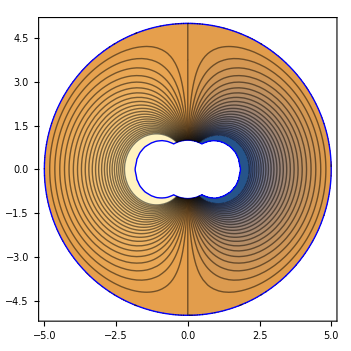

```mathematica
h=5;
r1:=√(x^2+y^2);
Q1:=ArcTan[x,y];
(*x=1.222;
y=0;
Dom[r1,Q1]

Domq[r1,Q1]/r1*)
ContourPlot[p[r1,Q1],{x,-h,h},{y,-h,h},RegionFunction->Function[{x,y,z},x^2+y^2>1 &&x^2+y^2<h^2 ],BoundaryStyle->Blue,Contours->50]
```

```mathematica
nn=100;
m=Table[0,{nn+1}];
r1=√(x^2+y^2);
Q1=ArcTan[x,y];
(*Print["x,  y,  ψ,  dψ/dr,  ω,  dω/dr"]*)
i=0;
r=1;
For[alf=0,alf<=Pi,alf+=Pi/nn,
i++;
x:=r Cos[alf]//N;
y:=r Sin[alf]//N;
(*Print[i," ", x,"   ",y,"   ",Floor[Psi[r1,alf],0.01],"   ",Floor[DPsi[r1,alf]//N,0.01],"   ",Floor[om[r1,alf]//N,0.01],"   ",Floor[Dom[r1,alf]//N,0.01]];*)
m[[i]]={Floor[x,0.0001],Floor[y,0.0001],Floor[Psi[r1,alf],0.0001],Floor[DPsi[r1,alf]//N,0.0001],Floor[om[r1,alf]//N,0.0001],Floor[Dom[r1,alf]//N,0.0001]};
]
ClearAll[x,y,i,r]
Export["C:\\Users\\Ислам\\Рабочий стол\\дипломная\\text.dat",m];
Export["C:\\Users\\Ислам\\Рабочий стол\\дипломная\\text.xls",m,"XLS"];
```

```mathematica
nr=100;
ClearAll[result];
result=Table[0,{nr+2}];
result[[1]]={"r","psi","dpsi","om","dom"};
alfa=Pi/2;
i=1;
For[r=1,r<=h,r+=(h-1)/nr,

i++;
(*Print[i," ", x,"   ",y,"   ",Floor[Psi[r1,alf],0.01],"   ",Floor[DPsi[r1,alf]//N,0.01],"   ",Floor[om[r1,alf]//N,0.01],"   ",Floor[Dom[r1,alf]//N,0.01]];*)
result[[i]]={Floor[r,0.0001],Floor[Psi[r,alfa],0.0001],Floor[DPsi[r,alfa]//N,0.0001],Floor[om[r,alfa]//N,0.0001],Floor[Dom[r,alfa]//N,0.0001]};
]
ClearAll[x,y,i,r]
Export["C:\\Users\\Ислам\\Рабочий стол\\дипломная\\fi_const_f=1.dat",result];
Export["C:\\Users\\Ислам\\Рабочий стол\\дипломная\\fi_const_f=1.xls",result,"XLS"];
```

```mathematica
nr=30;
ClearAll[result];
result=Table[0,{nr+2}];
result[[1]]={"r","psi","dpsi","om","dom"};
alfa=Pi/2;
i=1;
For[r=1,r<=h,r+=(h-1)/nr,

i++;
(*Print[i," ", x,"   ",y,"   ",Floor[Psi[r1,alf],0.01],"   ",Floor[DPsi[r1,alf]//N,0.01],"   ",Floor[om[r1,alf]//N,0.01],"   ",Floor[Dom[r1,alf]//N,0.01]];*)
result[[i]]={Floor[r,0.0001],Floor[Psi[r,alfa],0.0001],Floor[DPsi[r,alfa]//N,0.0001],Floor[om[r,alfa]//N,0.0001],Floor[Dom[r,alfa]//N,0.0001]};
]
ClearAll[x,y,i,r]
Export["C:\\Users\\Ислам\\Рабочий стол\\дипломная\\fi_const_f=1rrr.dat",result];
Export["C:\\Users\\Ислам\\Рабочий стол\\дипломная\\fi_const_f=1rrr.xls",result,"XLS"];
```

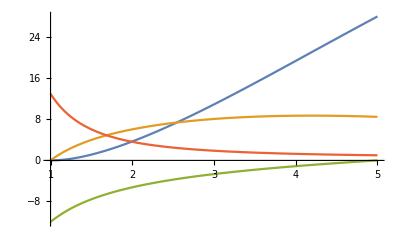

```mathematica
Plot[{Psi[r,Pi/2],DPsi[r,Pi/2],om[r,Pi/2],Dom[r,Pi/2]},{r,1,h}]
```